```mathematica
ClearAll["Global`*"]
```

Note, most of the work in this notebook comes from an already existing notebook located here: /Users/alexanderpickston/Dropbox (Heriot-Watt University Team)/RES_EPS_EMQL/userFolders/Alex/Graphs/model_graphStates/model_statePurity.nb

# Graph verification via smaller distilled states

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/alexanderpickston/Documents/GitHub/QIPmma/Graph states

## Preliminary settings

### Imports

```mathematica
Import[NotebookDirectory[]<>"QIPmma.m"]
Import[NotebookDirectory[]<>"library_graphStates.m"]
```

### Definitions

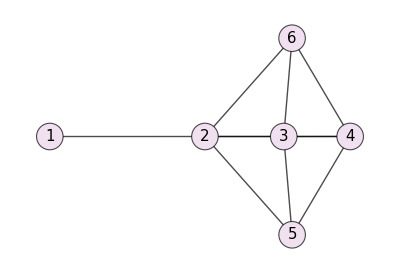
```mathematica
tridentGraph=-Graphics-;LC4graph=-Graphics-;
```

```mathematica
userColor=Lighter@Gray;
networkColor=White;
CustomGraphStyle[graph_]:=Graph[graph,VertexStyle->{1->Directive[EdgeForm[{Thick,Opacity[1],Black}],userColor],2->Directive[EdgeForm[{Thick,Opacity[1],Black}],userColor],5->Directive[EdgeForm[{Thick,Opacity[1],Black}],userColor],6->Directive[EdgeForm[{Thick,Opacity[1],Black}],userColor],4->Directive[EdgeForm[{Thick,Opacity[1],Black}],networkColor],3->Directive[EdgeForm[{Thick,Opacity[1],Black}],networkColor]},VertexLabelStyle->Directive[Black,FontFamily->"IBM Plex Serif",25],EdgeStyle->Directive[Black,Thick,Opacity[1]],GraphLayout->"CircularEmbedding"];
```

Tracing out qubits from a quantum state

```mathematica
(* Partial Trace - adapted from Mark S. Tame, http://library.wolfram.com/infocenter/MathSource/5571/ *)
SwapParts[expr_, pos1_, pos2_] := ReplacePart[#,#, {pos1,pos2}, {pos2,pos1}]&[expr];
TraceSystem[dm_, sys_]:=Block[{Qubits,TrkM,n,M,k,Permut,perm,b,c,p},
Qubits=Reverse[Sort[sys]];(* rearrange the list of qubits to be traced out *)
TrkM=dm;

(* For all qubits to be traced out... *)
For[q=1,q≤Dimensions[Qubits][[1]],q++,
n=Log[2,(Dimensions[TrkM][[1]])]; (* dimensions of original system *)
M=TrkM;
k=Qubits[[q]];

If[k==n,(* if tracing the last system *)
TrkM={};
For[p=1,p<2^n+1,p=p+2,
TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];(* Pick row p/p+1 and take elements 1/2 through 2^n in steps of 2 - sum thoese and append to zero matrix - do for all rows *)
 ],

For[j=0,j<(n-k),j++,(* if not - permute accordingly *)
b={0};
For[i=1,i<2^n+1,i++,
If[(Mod[(IntegerDigits[i-1,2,n][[n]]+IntegerDigits[i-1,2,n][[n-j-1]]),2])==1 && Count[b, i]  ==0, Permut={i,(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)};
b=Append[b,(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)];
c=Range[2^n];
perm=SwapParts[c,{i},{(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)}];

M=M[[perm,perm]];

 ]    
];
(* and now trace out last system *)
TrkM={};
For[p=1,p<2^n+1,p=p+2,
TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];
]
   ]
];

];
Clear[Qubits,n,M,k,Permut,perm,b,c];
TrkM
];
```

## Defining states

### Experimental state generated on bench

```mathematica
expψ={{1/(2 √2)},{0},{0},{-1/(2 √2)},{0},{0},{0},{0},{0},{0},{0},{0},{-1/(2 √2)},{0},{0},{-1/(2 √2)},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{-1/(2 √2)},{0},{0},{1/(2 √2)},{0},{0},{0},{0},{0},{0},{0},{0},{-1/(2 √2)},{0},{0},{-1/(2 √2)}};
```

```mathematica
expρ=DensityMatrix[expψ];
```

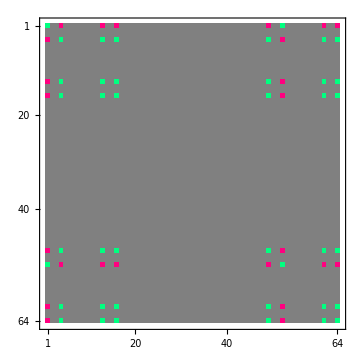

```mathematica
MatrixPlot[expρ,ColorFunction->(RGBColor[1-#,#,1/2]&)]
```

### Theoretical state of trident

```mathematica
theoryψTrident=Import["_output_states/output_state_trident_updatedcz.csv"];
theoryψTrident=ToExpression/@theoryψTrident
```

{{0.125},{0.125},{0.125},{-0.125},{0.125},{-0.125},{0.125},{0.125},{0.125},{0.125},{0.125},{-0.125},{-0.125},{0.125},{-0.125},{-0.125},{0.125},{0.125},{0.125},{-0.125},{-0.125},{0.125},{-0.125},{-0.125},{0.125},{0.125},{0.125},{-0.125},{0.125},{-0.125},{0.125},{0.125},{0.125},{0.125},{0.125},{-0.125},{0.125},{-0.125},{0.125},{0.125},{0.125},{0.125},{0.125},{-0.125},{-0.125},{0.125},{-0.125},{-0.125},{-0.125},{-0.125},{-0.125},{0.125},{0.125},{-0.125},{0.125},{0.125},{-0.125},{-0.125},{-0.125},{0.125},{-0.125},{0.125},{-0.125},{-0.125}}

```mathematica
theoryρTrident=DensityMatrix[theoryψTrident];
```

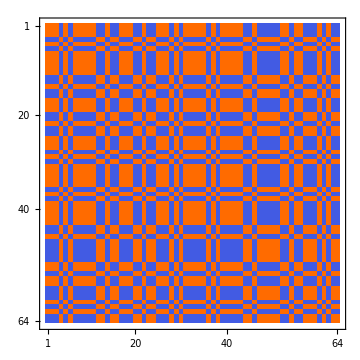

```mathematica
MatrixPlot[theoryρTrident]
```

### Theoretical state of graph before GHZ

```mathematica
theoryψLC4=Import["_output_states/output_state_LC4_correct.csv"];
theoryψLC4=ToExpression/@theoryψLC4
```

{{0.125},{0.125},{0.125},{0.125},{0.125},{-0.125},{-0.125},{0.125},{0.125},{-0.125},{-0.125},{0.125},{-0.125},{-0.125},{-0.125},{-0.125},{0.125},{-0.125},{-0.125},{0.125},{-0.125},{-0.125},{-0.125},{-0.125},{-0.125},{-0.125},{-0.125},{-0.125},{-0.125},{0.125},{0.125},{-0.125},{0.125},{0.125},{0.125},{0.125},{0.125},{-0.125},{-0.125},{0.125},{0.125},{-0.125},{-0.125},{0.125},{-0.125},{-0.125},{-0.125},{-0.125},{-0.125},{0.125},{0.125},{-0.125},{0.125},{0.125},{0.125},{0.125},{0.125},{0.125},{0.125},{0.125},{0.125},{-0.125},{-0.125},{0.125}}

```mathematica
theoryρLC4=DensityMatrix@theoryψLC4;
```

### Experimental state rotated to trident

```mathematica
expψRotated=Kronk[{Hada,sz,Hada,sz,Hada,sz}].expψ;
expρRotated=DensityMatrix[expψRotated];
```

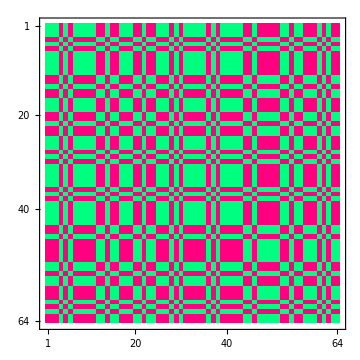

```mathematica
MatrixPlot[expρRotated,ColorFunction->(RGBColor[1-#,#,1/2]&)]
```

#### Checking states are correct

```mathematica
Fidelity[expρRotated,theoryρTrident]
```

1.

## Noise

### Failed fusion noise

```mathematica
failedFusionState=Kronk[{DensityMatrix[1/(√2)(hh+vv)],DensityMatrix[dd],DensityMatrix[1/(√2)(hh+vv)]}];
```

```mathematica
Tr[failedFusionState]
```

1

```mathematica
NoiseFailedFusions[ρ_,p_]:=(1/(1+p)*ρ)+(p/(1+p)*failedFusionState)
```

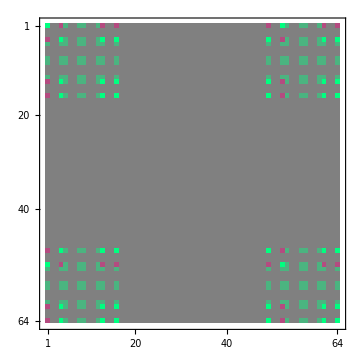

```mathematica
MatrixPlot[NoiseFailedFusions[expρ,1],ColorFunction->(RGBColor[1-#,#,1/2]&)]
```

## Trident to GHZ state

First operations to apply to the experimentally rotated state is to get to the LC equivalent graph that measurements are performed upon. We require to transform the starting state via LC operations on qubits 6 and 4.

Operating on the trident → LC6 equivalent → LC4 equivalent and then measuring Z3 and Z4

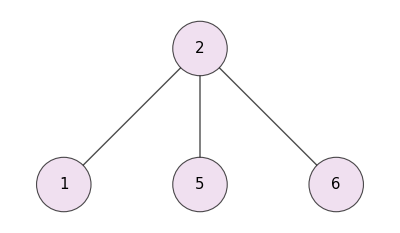
```mathematica
GraphicsRow[{CustomGraphStyle@tridentGraph,CustomGraphStyle@LC4graph,CustomGraphStyle@-Graphics-},ImageSize->500]
```

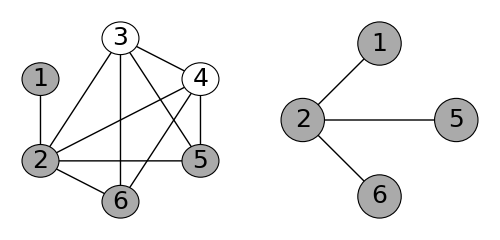

```mathematica
LC6=Kron[s0,s0,s0,neighborhoodLC,neighborhoodLC,vertexLC];
LC4=Kron[s0,neighborhoodLC,neighborhoodLC,vertexLC,neighborhoodLC,neighborhoodLC];
```

```mathematica
expψRotatedLC6LC4=LC4.(LC6.expψRotated);
expρRotatedLC6LC4=DensityMatrix[expψRotatedLC6LC4];
```

```mathematica
Fidelity[theoryρLC4,expρRotatedLC6LC4]
```

1.

### Density matrix of GHZ after measurements on qubits 3 and 4

-Graphics-

```mathematica
m=Kronk[{s0,s0,DensityMatrix[h],DensityMatrix[h],s0,s0}];
expρRotatedLC6LC4Z3Z4=(m.expρRotatedLC6LC4.m†)/Tr[m†.m.expρRotatedLC6LC4];
```

```mathematica
expρRotatedLC6LC4Z3Z4GHZequiv=TraceSystem[expρRotatedLC6LC4Z3Z4,{3,4}];
```

```mathematica
expρRotatedLC6LC4Z3Z4GHZ=Kronk[{Hada,s0,Hada,Hada}].expρRotatedLC6LC4Z3Z4GHZequiv.Kronk[{Hada,s0,Hada,Hada}]†;
```

```mathematica
DensityMatrixPlotLabels[4]
DensityMatrixPlot[expρRotatedLC6LC4Z3Z4GHZ]
```

-Graphics3D-

## Noise analysis

#### Noise definition

```mathematica
DepolarisingNoise[state_,p_,dim_]:=(p/2)*IdentityMatrix[dim]/Tr[IdentityMatrix[dim]]+(1-p)*state
```

```mathematica
steps=Range[0,1,0.01];
DepolNoiseexpρRotatedLC6LC4=Table[DepolarisingNoise[expρRotatedLC6LC4,i,64],{i,steps}];
```

```mathematica
Purity/@DepolNoiseexpρRotatedLC6LC4
```

{1.,0.980255,0.960708,0.941358,0.922206,0.903252,0.884495,0.865936,0.847575,0.829411,0.811445,0.793677,0.776106,0.758733,0.741558,0.72458,0.7078,0.691218,0.674833,0.658646,0.642656,0.626864,0.61127,0.595874,0.580675,0.565674,0.55087,0.536264,0.521856,0.507646,0.493633,0.479818,0.4662,0.45278,0.439558,0.426533,0.413706,0.401077,0.388645,0.376411,0.364375,0.352536,0.340895,0.329452,0.318206,0.307158,0.296308,0.285655,0.2752,0.264943,0.254883,0.245021,0.235356,0.225889,0.21662,0.207549,0.198675,0.189999,0.18152,0.173239,0.165156,0.157271,0.149583,0.142093,0.1348,0.127705,0.120808,0.114108,0.107606,0.101302,0.0951953,0.0892863,0.083575,0.0780613,0.0727453,0.067627,0.0627062,0.0579832,0.0534578,0.0491301,0.045,0.0410676,0.0373328,0.0337957,0.0304563,0.0273145,0.0243703,0.0216238,0.019075,0.0167238,0.0145703,0.0126145,0.0108562,0.0092957,0.00793281,0.00676758,0.0058,0.00503008,0.00445781,0.0040832,0.00390625}

#### Density matrix after measurements on qubits 3 and 4

```mathematica
m=Kronk[{s0,s0,DensityMatrix[h],DensityMatrix[h],s0,s0}];
expρRotatedLC6LC4Z3Z4=(m.#.m†)/Tr[m†.m.#]&/@DepolNoiseexpρRotatedLC6LC4;
```

```mathematica
expρRotatedLC6LC4Z3Z4GHZequiv=TraceSystem[#,{3,4}]&/@expρRotatedLC6LC4Z3Z4;
```

```mathematica
expρRotatedLC6LC4Z3Z4GHZ=(Kronk[{Hada,s0,Hada,Hada}].#.Kronk[{Hada,s0,Hada,Hada}]†)&/@expρRotatedLC6LC4Z3Z4GHZequiv;
```

```mathematica
Purity/@expρRotatedLC6LC4Z3Z4GHZ
```

{1.,0.990602,0.981156,0.971664,0.962125,0.952539,0.942907,0.933228,0.923503,0.913731,0.903913,0.894049,0.884139,0.874183,0.864182,0.854136,0.844045,0.83391,0.823731,0.813507,0.803241,0.792931,0.78258,0.772186,0.761751,0.751276,0.74076,0.730205,0.719612,0.708981,0.698313,0.687609,0.676871,0.666098,0.655293,0.644456,0.633589,0.622692,0.611768,0.600818,0.589844,0.578846,0.567828,0.55679,0.545735,0.534664,0.523581,0.512487,0.501385,0.490277,0.479167,0.468056,0.456949,0.445847,0.434756,0.423677,0.412616,0.401575,0.39056,0.379574,0.368622,0.35771,0.346842,0.336023,0.32526,0.314558,0.303923,0.293364,0.282886,0.272497,0.262204,0.252017,0.241943,0.231993,0.222175,0.2125,0.202979,0.193622,0.184443,0.175453,0.166667,0.158097,0.149759,0.141669,0.133844,0.1263,0.119056,0.112132,0.105548,0.0993274,0.0934917,0.088066,0.0830761,0.0785494,0.074515,0.0710034,0.0680473,0.0656813,0.0639418,0.0628676,0.0625}

## 4-GHZ to 3-GHZ

## Trident to Bell states

First operations to apply to the experimentally rotated state is to get to the LC equivalent graph that measurements are performed upon. We require to transform the starting state via LC operations on qubits 6 and 4.

Operating on the trident → LC6 equivalent → LC4 equivalent and then measuring Z4 and Y3

#### Density matrix after measurements on qubits 3 and 4

```mathematica
m=Kronk[{s0,s0,DensityMatrix[h],DensityMatrix[r],s0,s0}];

expρRotatedZ3Y4Bell=(m.expρRotatedLC6LC4.m†)/Tr[m†.m.expρRotatedLC6LC4];
```

Bell_12

```mathematica
expρRotatedZ3Y4Bell12=TraceSystem[expρRotatedZ3Y4Bell,{3,4,5,6}];
expρRotatedZ3Y4Bell12=Abs[Kronk[{Hada,s0}].expρRotatedZ3Y4Bell12.Kronk[{Hada,s0}]†]
```

{{1/2,0,0,1/2},{0,0,0,0},{0,0,0,0},{1/2,0,0,1/2}}

Bell_56

```mathematica
expρRotatedZ3Y4Bell56=TraceSystem[expρRotatedZ3Y4Bell,{1,2,3,4}];
expρRotatedZ3Y4Bell56=Abs[Kronk[{Hada,Hada}].expρRotatedZ3Y4Bell56.Kronk[{Hada,Hada}]†]
```

{{1/2,0,0,1/2},{0,0,0,0},{0,0,0,0},{1/2,0,0,1/2}}

#### Density matrix after measurements on qubits 3 and 4 - Alternative starting state

```mathematica
m=Kronk[{s0,s0,DensityMatrix[h],DensityMatrix[r],s0,s0}];

expρRotatedZ3Y4Bell=(m.expρRotated.m†)/Tr[m†.m.expρRotated];
```

#### Bell_12

```mathematica
expρRotatedZ3Y4Bell12=TraceSystem[expρRotatedZ3Y4Bell,{3,4,5,6}];
expρRotatedZ3Y4Bell12=Abs[Kronk[{Hada,Hada}].expρRotatedZ3Y4Bell12.Kronk[{Hada,Hada}]†]
```

{{1/4,1/4,0,0},{1/4,1/4,0,0},{0,0,1/4,1/4},{0,0,1/4,1/4}}

#### Bell_56

```mathematica
expρRotatedZ3Y4Bell56=TraceSystem[expρRotatedZ3Y4Bell,{1,2,3,4}];
expρRotatedZ3Y4Bell56=Abs[Kronk[{Hada,Hada}].expρRotatedZ3Y4Bell56.Kronk[{Hada,Hada}]†]
```

{{1/4,1/4,0,0},{1/4,1/4,0,0},{0,0,1/4,1/4},{0,0,1/4,1/4}}

#### Bell_26

## Noise analysis - with all plots

#### Noise definition

```mathematica
DepolarisingNoise[state_,p_,dim_]:=(p/2)*IdentityMatrix[dim]/Tr[IdentityMatrix[dim]]+(1-p)*state
```

```mathematica
steps=Range[0,1,0.01];
DepolNoiseexpρRotatedLC6LC4=Table[DepolarisingNoise[expρRotatedLC6LC4,i,64],{i,steps}];
```

```mathematica
Purity/@DepolNoiseexpρRotatedLC6LC4
```

{1.,0.980255,0.960708,0.941358,0.922206,0.903252,0.884495,0.865936,0.847575,0.829411,0.811445,0.793677,0.776106,0.758733,0.741558,0.72458,0.7078,0.691218,0.674833,0.658646,0.642656,0.626864,0.61127,0.595874,0.580675,0.565674,0.55087,0.536264,0.521856,0.507646,0.493633,0.479818,0.4662,0.45278,0.439558,0.426533,0.413706,0.401077,0.388645,0.376411,0.364375,0.352536,0.340895,0.329452,0.318206,0.307158,0.296308,0.285655,0.2752,0.264943,0.254883,0.245021,0.235356,0.225889,0.21662,0.207549,0.198675,0.189999,0.18152,0.173239,0.165156,0.157271,0.149583,0.142093,0.1348,0.127705,0.120808,0.114108,0.107606,0.101302,0.0951953,0.0892863,0.083575,0.0780613,0.0727453,0.067627,0.0627062,0.0579832,0.0534578,0.0491301,0.045,0.0410676,0.0373328,0.0337957,0.0304563,0.0273145,0.0243703,0.0216238,0.019075,0.0167238,0.0145703,0.0126145,0.0108562,0.0092957,0.00793281,0.00676758,0.0058,0.00503008,0.00445781,0.0040832,0.00390625}

#### Density matrix of both Bell states after measurements on qubits 3 and 4

```mathematica
m=Kronk[{s0,s0,DensityMatrix[h],DensityMatrix[r],s0,s0}];
expρRotatedLC6LC4Z3Y4=(m.#.m†)/Tr[m†.m.#]&/@DepolNoiseexpρRotatedLC6LC4;
```

```mathematica
expρRotatedZ3Y4Bell12=TraceSystem[#,{3,4,5,6}]&/@expρRotatedLC6LC4Z3Y4;
expρRotatedLC6LC4Z3Y4Bell12=(Kronk[{Hada,Hada}].#.Kronk[{Hada,Hada}]†)&/@expρRotatedZ3Y4Bell12;
```

```mathematica
expρRotatedZ3Y4Bell56=TraceSystem[#,{1,2,3,4}]&/@expρRotatedLC6LC4Z3Y4;
expρRotatedLC6LC4Z3Y4Bell56=Abs[(Kronk[{Hada,Hada}].#.Kronk[{Hada,Hada}]†)&/@expρRotatedZ3Y4Bell56];
```

```mathematica
Purity/@expρRotatedLC6LC4Z3Y4Bell12
```

{1.+0. ⅈ,0.992481+0. ⅈ,0.984925+0. ⅈ,0.977331+0. ⅈ,0.9697+0. ⅈ,0.962032+0. ⅈ,0.954326+0. ⅈ,0.946582+0. ⅈ,0.938802+0. ⅈ,0.930985+0. ⅈ,0.92313+0. ⅈ,0.915239+0. ⅈ,0.907311+0. ⅈ,0.899347+0. ⅈ,0.891346+0. ⅈ,0.883309+0. ⅈ,0.875236+0. ⅈ,0.867128+0. ⅈ,0.858984+0. ⅈ,0.850806+0. ⅈ,0.842593+0. ⅈ,0.834345+0. ⅈ,0.826064+0. ⅈ,0.817749+0. ⅈ,0.809401+0. ⅈ,0.80102+0. ⅈ,0.792608+0. ⅈ,0.784164+0. ⅈ,0.77569+0. ⅈ,0.767185+0. ⅈ,0.758651+0. ⅈ,0.750088+0. ⅈ,0.741497+0. ⅈ,0.732879+0. ⅈ,0.724234+0. ⅈ,0.715565+0. ⅈ,0.706871+0. ⅈ,0.698154+0. ⅈ,0.689415+0. ⅈ,0.680655+0. ⅈ,0.671875+0. ⅈ,0.663077+0. ⅈ,0.654262+0. ⅈ,0.645432+0. ⅈ,0.636588+0. ⅈ,0.627732+0. ⅈ,0.618865+0. ⅈ,0.60999+0. ⅈ,0.601108+0. ⅈ,0.592222+0. ⅈ,0.583333+0. ⅈ,0.574445+0. ⅈ,0.565559+0. ⅈ,0.556678+0. ⅈ,0.547804+0. ⅈ,0.538942+0. ⅈ,0.530093+0. ⅈ,0.52126+0. ⅈ,0.512448+0. ⅈ,0.503659+0. ⅈ,0.494898+0. ⅈ,0.486168+0. ⅈ,0.477473+0. ⅈ,0.468818+0. ⅈ,0.460208+0. ⅈ,0.451646+0. ⅈ,0.443139+0. ⅈ,0.434691+0. ⅈ,0.426309+0. ⅈ,0.417997+0. ⅈ,0.409763+0. ⅈ,0.401613+0. ⅈ,0.393555+0. ⅈ,0.385594+0. ⅈ,0.37774+0. ⅈ,0.37+0. ⅈ,0.362383+0. ⅈ,0.354898+0. ⅈ,0.347554+0. ⅈ,0.340363+0. ⅈ,0.333333+0. ⅈ,0.326478+0. ⅈ,0.319808+0. ⅈ,0.313336+0. ⅈ,0.307075+0. ⅈ,0.30104+0. ⅈ,0.295245+0. ⅈ,0.289706+0. ⅈ,0.284439+0. ⅈ,0.279462+0. ⅈ,0.274793+0. ⅈ,0.270453+0. ⅈ,0.266461+0. ⅈ,0.26284+0. ⅈ,0.259612+0. ⅈ,0.256803+0. ⅈ,0.254438+0. ⅈ,0.252545+0. ⅈ,0.251153+0. ⅈ,0.250294+0. ⅈ,0.25+0. ⅈ}

### Plots

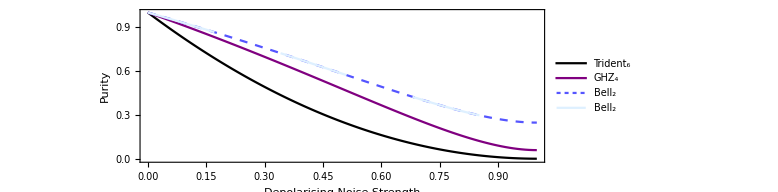

```mathematica
ListLinePlot[{{steps,Purity/@DepolNoiseexpρRotatedLC6LC4}ᵀ,{steps,Purity/@expρRotatedLC6LC4Z3Z4GHZ}ᵀ,{steps,Purity/@expρRotatedLC6LC4Z3Y4Bell12}ᵀ,{steps,Purity/@expρRotatedLC6LC4Z3Y4Bell56}ᵀ}
,PlotStyle->{Black
			,Purple
			,Directive[Lighter@Blue,Dashing[0.01]]
			,Directive[LightBlue,Dashing[0.2]]}
,PlotLegends->{"Trident_6","GHZ_4","Bell_2","Bell_2"}
,FrameLabel->{"Depolarising Noise Strength (p)","Purity"}
,AspectRatio->1/3
,ImageSize->Large]
```

### Failed fusion noise

```mathematica
steps=Range[0,1,0.01];
failedFusionNoiseExpρRotatedLC6LC4=Table[NoiseFailedFusions[expρRotatedLC6LC4,i],{i,steps}];
```

#### GHZ - Density matrix after measurements on qubits 3 and 4

```mathematica
m=Kronk[{s0,s0,DensityMatrix[h],DensityMatrix[h],s0,s0}];
expρRotatedLC6LC4Z3Z4=(m.#.m†)/Tr[m†.m.#]&/@failedFusionNoiseExpρRotatedLC6LC4;
```

```mathematica
expρRotatedLC6LC4Z3Z4GHZequiv=TraceSystem[#,{3,4}]&/@expρRotatedLC6LC4Z3Z4;
```

```mathematica
expρRotatedLC6LC4Z3Z4GHZ=(Kronk[{Hada,s0,Hada,Hada}].#.Kronk[{Hada,s0,Hada,Hada}]†)&/@expρRotatedLC6LC4Z3Z4GHZequiv;
```

```mathematica
Purity/@expρRotatedLC6LC4Z3Z4GHZ
```

{1.,0.980394,0.961553,0.943444,0.926036,0.909297,0.8932,0.877719,0.862826,0.848498,0.834711,0.821443,0.808673,0.796382,0.784549,0.773157,0.762188,0.751625,0.741454,0.731657,0.722222,0.713134,0.704381,0.695948,0.687825,0.68,0.672462,0.665199,0.658203,0.651463,0.64497,0.638716,0.632691,0.626887,0.621297,0.615912,0.610727,0.605733,0.600924,0.596294,0.591837,0.587546,0.583416,0.579442,0.575617,0.571938,0.568399,0.564996,0.561724,0.558578,0.555556,0.552651,0.549861,0.547183,0.544611,0.542144,0.539776,0.537507,0.535331,0.533246,0.53125,0.529339,0.527511,0.525763,0.524093,0.522498,0.520975,0.519524,0.518141,0.516824,0.515571,0.51438,0.51325,0.512179,0.511164,0.510204,0.509298,0.508443,0.507638,0.506882,0.506173,0.50551,0.504891,0.504315,0.503781,0.503287,0.502833,0.502416,0.502037,0.501694,0.501385,0.50111,0.500868,0.500658,0.500478,0.500329,0.500208,0.500116,0.500051,0.500013,0.5}

#### Bell - Density matrix after measurements on qubits 3 and 4

```mathematica
(* Measurement operation for distilling Bell pairs between 1, 2 and 5, 6. *)
m=Kronk[{s0,s0,DensityMatrix[h],DensityMatrix[r],s0,s0}];
expρRotatedLC6LC4Z3Y4=(m.#.m†)/Tr[m†.m.#]&/@failedFusionNoiseExpρRotatedLC6LC4;
```

```mathematica
expρRotatedLC6LC4Z3Y4⟦1⟧
```

{{0.03125+0. ⅈ,0.-0.03125 ⅈ,0.-0.03125 ⅈ,0.03125+0. ⅈ,0.-0.03125 ⅈ,-0.03125+0. ⅈ,-0.03125+0. ⅈ,0.-0.03125 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-0.03125 ⅈ,-0.03125+0. ⅈ,-0.03125+0. ⅈ,0.-0.03125 ⅈ,-0.03125+0. ⅈ,0.+0.03125 ⅈ,0.+0.03125 ⅈ,-0.03125+0. ⅈ,0.+0. ⅈ,15,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0.03125 ⅈ,0.03125+0. ⅈ,0.03125+0. ⅈ,0.+0.03125 ⅈ,0.03125+0. ⅈ,0.-0.03125 ⅈ,0.-0.03125 ⅈ,0.03125+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},62,{1}}
 |  |  |  |

```mathematica
expρRotatedLC6LC4Z3Y4Bell12=TraceSystem[#,{3,4,5,6}]&/@expρRotatedLC6LC4Z3Y4;
expρRotatedLC6LC4Z3Y4Bell56=TraceSystem[#,{1,2,3,4}]&/@expρRotatedLC6LC4Z3Y4;
```

```mathematica
expρRotatedZ3Y4Bell12=Abs[Kronk[{Hada,s0}].#.Kronk[{Hada,s0}]†]&/@expρRotatedLC6LC4Z3Y4Bell12;
expρRotatedZ3Y4Bell56=Abs[Kronk[{Hada,Hada}].#.Kronk[{Hada,Hada}]†]&/@expρRotatedLC6LC4Z3Y4Bell56;
```

```mathematica
Purity/@expρRotatedZ3Y4Bell12
Purity/@expρRotatedZ3Y4Bell56
```

{1.,0.985296,0.971165,0.957583,0.944527,0.931973,0.9199,0.908289,0.897119,0.886373,0.876033,0.866082,0.856505,0.847286,0.838412,0.829868,0.821641,0.813719,0.80609,0.798743,0.791667,0.784851,0.778285,0.771961,0.765869,0.76,0.754346,0.748899,0.743652,0.738597,0.733728,0.729037,0.724518,0.720165,0.715972,0.711934,0.708045,0.7043,0.700693,0.697221,0.693878,0.690659,0.687562,0.684581,0.681713,0.678954,0.676299,0.673747,0.671293,0.668934,0.666667,0.664488,0.662396,0.660387,0.658458,0.656608,0.654832,0.65313,0.651498,0.649935,0.648437,0.647004,0.645633,0.644322,0.64307,0.641873,0.640732,0.639643,0.638605,0.637618,0.636678,0.635785,0.634938,0.634134,0.633373,0.632653,0.631973,0.631332,0.630728,0.630161,0.62963,0.629132,0.628668,0.628236,0.627836,0.627465,0.627125,0.626812,0.626528,0.62627,0.626039,0.625833,0.625651,0.625493,0.625359,0.625247,0.625156,0.625087,0.625038,0.625009,0.625}

{1.,0.990197,0.980777,0.971722,0.963018,0.954649,0.9466,0.938859,0.931413,0.924249,0.917355,0.910722,0.904337,0.898191,0.892275,0.886578,0.881094,0.875813,0.870727,0.865829,0.861111,0.856567,0.85219,0.847974,0.843913,0.84,0.836231,0.8326,0.829102,0.825732,0.822485,0.819358,0.816345,0.813443,0.810648,0.807956,0.805363,0.802866,0.800462,0.798147,0.795918,0.793773,0.791708,0.789721,0.787809,0.785969,0.7842,0.782498,0.780862,0.779289,0.777778,0.776326,0.774931,0.773591,0.772306,0.771072,0.769888,0.768753,0.767665,0.766623,0.765625,0.76467,0.763756,0.762882,0.762046,0.761249,0.760488,0.759762,0.75907,0.758412,0.757785,0.75719,0.756625,0.756089,0.755582,0.755102,0.754649,0.754221,0.753819,0.753441,0.753086,0.752755,0.752445,0.752157,0.75189,0.751644,0.751416,0.751208,0.751019,0.750847,0.750693,0.750555,0.750434,0.750329,0.750239,0.750164,0.750104,0.750058,0.750026,0.750006,0.75}

```mathematica
expρRotatedZ3Y4Bell12⟦1⟧
```

{{0.5,0.,0.,0.5},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.5,0.,0.,0.5}}

```mathematica
Fidelity[expρRotatedZ3Y4Bell12⟦1⟧,DensityMatrix[1/(√2)(hh+vv)]]
Fidelity[expρRotatedZ3Y4Bell56⟦1⟧,DensityMatrix[1/(√2)(hh+vv)]]
```

1.

1.

### Plots

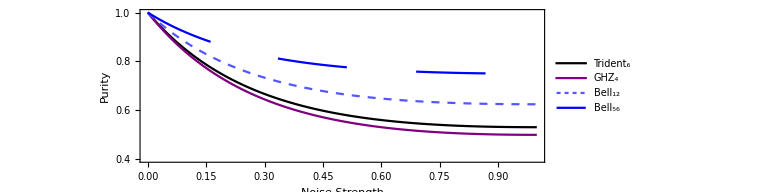

```mathematica
ListLinePlot[{{steps,Purity/@failedFusionNoiseExpρRotatedLC6LC4}ᵀ,{steps,Purity/@expρRotatedLC6LC4Z3Z4GHZ}ᵀ,{steps,Purity/@expρRotatedZ3Y4Bell12}ᵀ,{steps,Purity/@expρRotatedZ3Y4Bell56}ᵀ}
,PlotStyle->{Directive[Black,Thick]
			,Directive[Purple,Thick]
			,Directive[Lighter@Blue,Thick,Dashing[0.01]]
			,Directive[Blue,Thick,Dashing[0.2]]}
,PlotLegends->{"Trident_6","GHZ_4","Bell_12","Bell_56"}
,FrameLabel->{"Noise Strength","Purity"}
,AspectRatio->1/3
,PlotRange->{0.4,1}
,ImageSize->Large]
```